# Test NNTracePlot

These tests require the standard test file resources folder to be downloaded from Git and available at Tests/_resources.

Updated 20160608

## Initialization

```mathematica
<<NounouW`
```

HokahokaW`
Thu 9 Jun 2016 19:44:32     [Mathematica: 10.4.1 for Microsoft Windows (64-bit) (April 11, 2016)]
     Current local repository path:   C:\prog\_w\HokahokaW\.git
     Current branch [hash]:  dev [126533ea69146d2bf85bdf97b6ec768a9cbcc322]
     Remote:  origin (https://ktakagaki@github.com/ktakagaki/HokahokaW.git)

NounouW`
Thu 9 Jun 2016 19:44:32     [Mathematica: 10.4.1 for Microsoft Windows (64-bit) (April 11, 2016)]
     Current local repository path:   C:\prog\_w\NounouW\.git
     Current branch [hash]:  master [cd6135fbbad0d75c0526afbbbed4c99fe6c89b7c]
     Remote:  origin (https://github.com/ktakagaki/NounouW.git)

Welcome to nounou, a Scala/Java adapter for neurophysiological data.
Last GIT info from file resource: NNGit.gson.txt
  + current HEAD is: 1a58c41332bd336e036338dfedc8b6c19c080f3e
  + current branch is: master
  + remote names are: https://github.com/ktakagaki/nounou.git, https://github.com/slentzen/nounou.git, https://github.com/dowa4213/nounou.git

```mathematica
resourceDataDirectory=FileNameJoin[{ParentDirectory[NotebookDirectory[]], "_resources","nounou","Neuralynx"}]
```

C:\prog\_w\NounouW\NounouW\Tests\_resources\nounou\Neuralynx

```mathematica
FileExistsQ[resourceDataDirectory]
```

True

## BG001 (short snippet)

```mathematica
tempDataFiles=FileNames["*.ncs",FileNameJoin[{resourceDataDirectory,"BG001","2016-05-11_16-34-20", "split","t0508_001", "segment 1","1-1"}]];
```

```mathematica
testBG001 = NNLoad[tempDataFiles]
```

«JavaObject[nounou.elements.data.NNDataChannelArray]»

```mathematica
NNPrintInfo[ testBG001, "Timing" ]
```

nounou.elements.traits.NNTiming(fs=32000.0, segmentCount=1, 1a58c41332)
==================================================
segment	samples (  mm:ss  ) (    s   )	   start Ts  (  hh:mm )
   0	      2560 (  0:00.08) (     0.1)	  3401478496 ( 0:00.00)

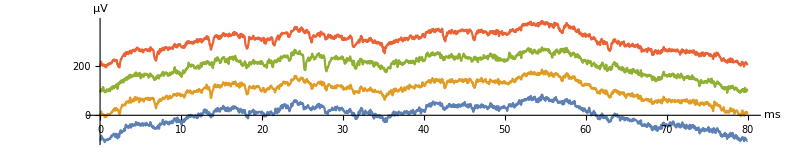

```mathematica
NNTracePlot[ testBG001, All, All, NNOptStack-> 100, AspectRatio-> 1/5, ImageSize-> 72*11]
```

## SPP010 (tetrode, one long segment)

```mathematica
testSPP010 = NNLoad[ FileNameJoin[{resourceDataDirectory,"SPP010","2013-12-02_17-07-31",#}]& /@{"Tet4a.ncs","Tet4b.ncs","Tet4c.ncs","Tet4d.ncs"} ]
```

«JavaObject[nounou.elements.data.NNDataChannelArray]»

```mathematica
NNPrintInfo[ testSPP010, "Timing" ]
```

nounou.elements.traits.NNTiming(fs=32000.0, segmentCount=1, 1a58c41332)
==================================================
segment	samples (  mm:ss  ) (    s   )	   start Ts  (  hh:mm )
   0	 151597056 ( 78:57.41) (  4737.4)	 19228868023 ( 0:00.00)

HHStackLists::invalidOptionValue: Option argument HHOptStack -> None is invalid.

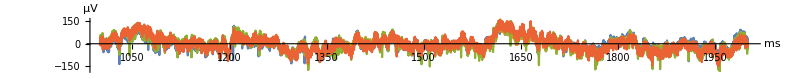

```mathematica
NNTracePlot[testSPP010, All, { 32001;;64000,0}, AspectRatio-> 1/10, ImageSize->11*72, NNOptStack-> None]
```

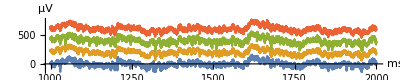

```mathematica
NNTracePlot[testSPP010, All, { 32001;;64000,0}, AspectRatio-> 1/5, ImageSize->Full, NNOptStack-> 200]
```

```mathematica
AbsoluteOptions[%, PlotRange]
```

{PlotRange→{{1000.03,2000.},{-141.291,761.266}}}

```mathematica
NNTracePlotManipulate[ testSPP010, All ]
```

## SPP010 (single channel, many segments)

### NNDataDownsample

```mathematica
testNCS1Downsample = NNDataDownsample[testNCS1, 8]
```

«JavaObject[nounou.elements.data.NNDataChannelExtracted]»

```mathematica
NNPrintInfo[ testNCS1Downsample ]
```

nounou.elements.data.NNDataChannelExtracted(94 segments, fs=4000.0, 3cc31723ae)

```mathematica
testDataFiltered = NNReadTrace[testNCS1Downsample,{ 4001;;8000,0} ];
```

```mathematica
ListLinePlot[testDataFiltered, AspectRatio-> 1/10, ImageSize->11*72]//Rasterize
```

-Graphics-

### NNDataDecimate

```mathematica
testNCS1Decimate = NNDataDecimate[testNCS1, 8]
```

«JavaObject[nounou.elements.data.NNDataChannelExtracted]»

```mathematica
NNPrintInfo[ testNCS1Decimate ]
```

nounou.elements.data.NNDataChannelExtracted(94 segments, fs=4000.0, 3cc31723ae)

```mathematica
testDataFiltered = NNReadTrace[testNCS1Decimate,{ 4001;;8000,0} ];
```

```mathematica
ListLinePlot[testDataFiltered, AspectRatio-> 1/10, ImageSize->11*72]//Rasterize
```

-Graphics-

### Whole Range Plot